# Calculus Univariate Calculus

## Optimization

```mathematica
L[theta_]:=1/Cos[theta]+2/Sin[theta]
```

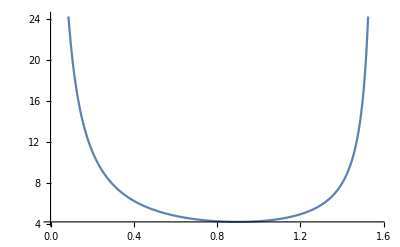

```mathematica
Plot[L[theta],{theta,0,Pi/2}]
```

```mathematica
L '[theta]
Solve[%==0,theta]
```

-2 Cot[theta] Csc[theta]+Sec[theta] Tan[theta]

{{theta→ConditionalExpression[-π-ArcTan[(-√(Root0.386Root[-1+3 #1-3 #1^2+5 #1^3&,1]0.38648820956430935)-2 (Root0.386Root[-1+3 #1-3 #1^2+5 #1^3&,1]0.38648820956430935)^(3/2)-5 (Root0.386Root[-1+3 #1-3 #1^2+5 #1^3&,1]0.38648820956430935)^(5/2))/(2 √(Root0.386Root[-1+3 #1-3 #1^2+5 #1^3&,1]0.38648820956430935))]+2 π C[1],C[1]∈ℤ]},{theta→ConditionalExpression[ArcTan[(√(Root0.386Root[-1+3 #1-3 #1^2+5 #1^3&,1]0.38648820956430935)+2 (Root0.386Root[-1+3 #1-3 #1^2+5 #1^3&,1]0.38648820956430935)^(3/2)+5 (Root0.386Root[-1+3 #1-3 #1^2+5 #1^3&,1]0.38648820956430935)^(5/2))/(2 √(Root0.386Root[-1+3 #1-3 #1^2+5 #1^3&,1]0.38648820956430935))]+2 π C[1],C[1]∈ℤ]},{theta→ConditionalExpression[π-ArcTan[(-√(Root0.107-0.711 ⅈRoot[-1+3 #1-3 #1^2+5 #1^3&,2]0.10675589521784531)-2 (Root0.107-0.711 ⅈRoot[-1+3 #1-3 #1^2+5 #1^3&,2]0.10675589521784531)^(3/2)-5 (Root0.107-0.711 ⅈRoot[-1+3 #1-3 #1^2+5 #1^3&,2]0.10675589521784531)^(5/2))/(2 √(Root0.107-0.711 ⅈRoot[-1+3 #1-3 #1^2+5 #1^3&,2]0.10675589521784531))]+2 π C[1],C[1]∈ℤ]},{theta→ConditionalExpression[ArcTan[(√(Root0.107-0.711 ⅈRoot[-1+3 #1-3 #1^2+5 #1^3&,2]0.10675589521784531)+2 (Root0.107-0.711 ⅈRoot[-1+3 #1-3 #1^2+5 #1^3&,2]0.10675589521784531)^(3/2)+5 (Root0.107-0.711 ⅈRoot[-1+3 #1-3 #1^2+5 #1^3&,2]0.10675589521784531)^(5/2))/(2 √(Root0.107-0.711 ⅈRoot[-1+3 #1-3 #1^2+5 #1^3&,2]0.10675589521784531))]+2 π C[1],C[1]∈ℤ]},{theta→ConditionalExpression[π-ArcTan[(-√(Root0.107+0.711 ⅈRoot[-1+3 #1-3 #1^2+5 #1^3&,3]0.10675589521784531)-2 (Root0.107+0.711 ⅈRoot[-1+3 #1-3 #1^2+5 #1^3&,3]0.10675589521784531)^(3/2)-5 (Root0.107+0.711 ⅈRoot[-1+3 #1-3 #1^2+5 #1^3&,3]0.10675589521784531)^(5/2))/(2 √(Root0.107+0.711 ⅈRoot[-1+3 #1-3 #1^2+5 #1^3&,3]0.10675589521784531))]+2 π C[1],C[1]∈ℤ]},{theta→ConditionalExpression[ArcTan[(√(Root0.107+0.711 ⅈRoot[-1+3 #1-3 #1^2+5 #1^3&,3]0.10675589521784531)+2 (Root0.107+0.711 ⅈRoot[-1+3 #1-3 #1^2+5 #1^3&,3]0.10675589521784531)^(3/2)+5 (Root0.107+0.711 ⅈRoot[-1+3 #1-3 #1^2+5 #1^3&,3]0.10675589521784531)^(5/2))/(2 √(Root0.107+0.711 ⅈRoot[-1+3 #1-3 #1^2+5 #1^3&,3]0.10675589521784531))]+2 π C[1],C[1]∈ℤ]}}

## Integral Evaluation

```mathematica
NIntegrate[x*ⅇ^(x^3),{x,0,1},WorkingPrecision->50]
```

0.78119703110865591510743281434829950577669739096218

```mathematica
Integrate[x*Sin[x]/(1+Cos[x]^2),{x,0,Pi}]
```

π^2/4

## Differential Equations

```mathematica
DSolve[y '[x]+y[x]/x==3x^2,y[x],x]
```

{{y[x]→(3 x^3)/4+C[1]/x}}

```mathematica
DSolve[y ''[x]-y'[x]-y[x]==0,y[x],x]
```

{{y[x]→ⅇ^((1/2-(√5)/2) x) C[1]+ⅇ^((1/2+(√5)/2) x) C[2]}}

## Parametric Equations, Alternative co-ordinates, and Other Esoteric Plotting Fun

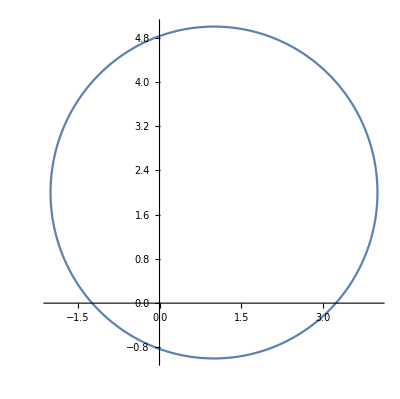

```mathematica
ParametricPlot[{1+3Cos[t],2+3Sin[t]},{t,0,2Pi}]
```

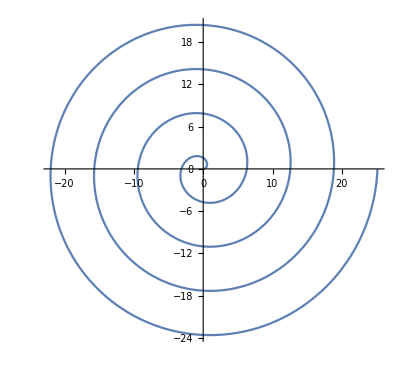

```mathematica
ParametricPlot[{t*Cos[t],t*Sin[t]},{t,0,8Pi}]
```

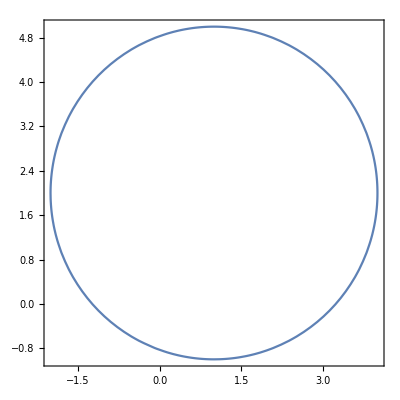

```mathematica
ContourPlot[(x-1)^2+(y-2)^2==9,{x,-2,4},{y,-1,5}]
```

```mathematica
PolarPlot[theta,{theta,0,8Pi}]
```

-Graphics-

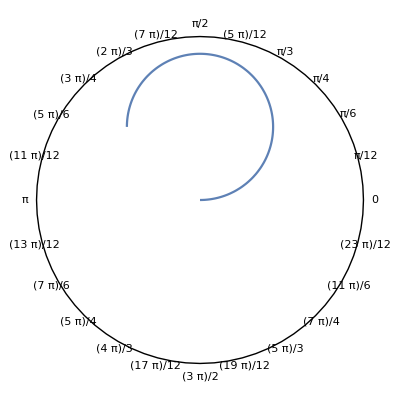

```mathematica
PolarPlot[Sin[theta],{theta,0,3Pi/4},PolarAxes->Automatic]
```

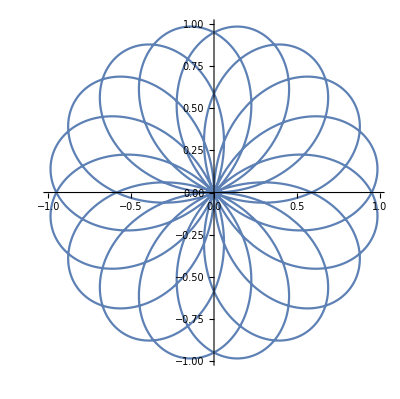

```mathematica
PolarPlot[Sin[8*theta/5],{theta,0,10Pi}]
```

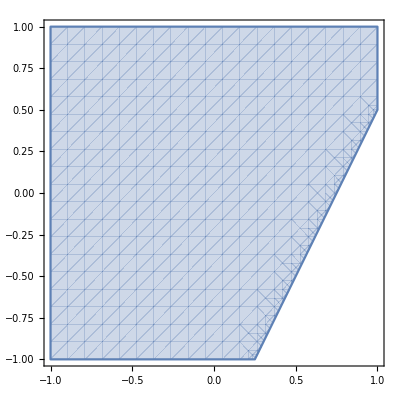

```mathematica
RegionPlot[4x-2y<3,{x,-1,1},{y,-1,1}]
```